#### Hyperbolic

```mathematica
Clear[H,f]
```

```mathematica
Clear[α,ν]
f[q_]:=(1+(α^2/Sinh[ν q]^2))^(1/2)
D[f[2 x],x]//Simplify
```

-(2 α^2 ν Coth[2 x ν] Csch[2 x ν]^2)/(√(1+α^2 Csch[2 x ν]^2))

```mathematica
H[q1_,q2_,p1_,p2_]:=(Cosh[p1]+Cosh[p2])f[q1-q2]
```

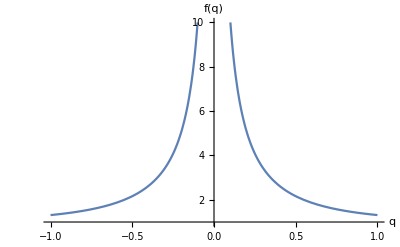

```mathematica
Plot[(1+(α^2/Sinh[x]^2))^(1/2)//.α->1,{x,-1,1},PlotRange->{1,10},AxesLabel->{"q","f(q)"},Axes->True, Ticks->False]
```

```mathematica
Manipulate[Plot[(1+(α^2/Sinh[2x]^2))^(1/2),{x,-1,1}],{α,0.1,2}]
```

```mathematica
(*Hamiltonian equations of motion*)
```

```mathematica
dx1=D[H[x1,x2,p1,p2],p1]//FullSimplify //Simplify
```

√(1+α^2 Csch[nu (x1-x2)]^2) Sinh[p1]

```mathematica
dp1=-D[H[x1,x2,p1,p2],x1] //FullSimplify
```

(nu α^2 (Cosh[p1]+Cosh[p2]) Coth[nu (x1-x2)] Csch[nu (x1-x2)]^2)/(√(1+α^2 Csch[nu (x1-x2)]^2))

```mathematica
(*Imposing symmetric motion*)
```

```mathematica
eq1=dx1/.{x1->x[t],x2->-x[t],p1->p[t],p2->-p[t]}//FullSimplify
```

√(1+α^2 Csch[2 nu x[t]]^2) Sinh[p[t]]

```mathematica
(*eq2=dp1/.{x1->x[t],x2->-x[t],p1->p[t],p2->-p[t]}//FullSimplify*)
```

(2 nu α^2 Cosh[p[t]] Coth[2 nu x[t]] Csch[2 nu x[t]]^2)/(√(1+α^2 Csch[2 nu x[t]]^2))

```mathematica
(2 α^2 Cosh[p[t]] Coth[2 x[t]] Csch[2 x[t]]^2)/(√(1+α^2 Csch[2 x[t]]^2));
(*This is not good, the correct factor is 4 instead of 2! It comes from the EOM for pdot: pdot=-2cosh(p) f'(2x), and from the argument 2x we get the other mult. factor of 2.*)
eq2=(4 α^2 Cosh[p[t]] Coth[2 x[t]] Csch[2 x[t]]^2)/(√(1+α^2 Csch[2 x[t]]^2));
```

```mathematica
(*Solving the diffeqs*)
```

```mathematica
DSolve[{eq1==x'[t],eq2==p'[t]},{x[t],p[t]},t]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x[t]→-1/2 ⅈ ArcSin[(ⅇ^(4 α^2 C[1]) α √Cosh[InverseFunction[(√Cosh[K[1]] √(ⅇ^(-8 α^2 C[1]) Sech[K[1]]))/((-1+ⅇ^(8 α^2 C[1]) Cosh[K[1]])^(3/2) √(1-(ⅇ^(8 α^2 C[1]) α^2 Cosh[K[1]])/(-1+ⅇ^(8 α^2 C[1]) Cosh[K[1]])))K[1]1#1&][-(4 ⅈ ⅇ^(-12 α^2 C[1]) t)/α+C[2]]])/(√(-1+ⅇ^(8 α^2 C[1]) Cosh[InverseFunction[(√Cosh[K[1]] √(ⅇ^(-8 α^2 C[1]) Sech[K[1]]))/((-1+ⅇ^(8 α^2 C[1]) Cosh[K[1]])^(3/2) √(1-(ⅇ^(8 α^2 C[1]) α^2 Cosh[K[1]])/(-1+ⅇ^(8 α^2 C[1]) Cosh[K[1]])))K[1]1#1&][-(4 ⅈ ⅇ^(-12 α^2 C[1]) t)/α+C[2]]]))],p[t]→InverseFunction[(√Cosh[K[1]] √(ⅇ^(-8 α^2 C[1]) Sech[K[1]]))/((-1+ⅇ^(8 α^2 C[1]) Cosh[K[1]])^(3/2) √(1-(ⅇ^(8 α^2 C[1]) α^2 Cosh[K[1]])/(-1+ⅇ^(8 α^2 C[1]) Cosh[K[1]])))K[1]1#1&][-(4 ⅈ ⅇ^(-12 α^2 C[1]) t)/α+C[2]]},{x[t]→1/2 ⅈ ArcSin[(ⅇ^(4 α^2 C[1]) α √Cosh[InverseFunction[(√Cosh[K[2]] √(ⅇ^(-8 α^2 C[1]) Sech[K[2]]))/((-1+ⅇ^(8 α^2 C[1]) Cosh[K[2]])^(3/2) √(1-(ⅇ^(8 α^2 C[1]) α^2 Cosh[K[2]])/(-1+ⅇ^(8 α^2 C[1]) Cosh[K[2]])))K[2]1#1&][(4 ⅈ ⅇ^(-12 α^2 C[1]) t)/α+C[2]]])/(√(-1+ⅇ^(8 α^2 C[1]) Cosh[InverseFunction[(√Cosh[K[2]] √(ⅇ^(-8 α^2 C[1]) Sech[K[2]]))/((-1+ⅇ^(8 α^2 C[1]) Cosh[K[2]])^(3/2) √(1-(ⅇ^(8 α^2 C[1]) α^2 Cosh[K[2]])/(-1+ⅇ^(8 α^2 C[1]) Cosh[K[2]])))K[2]1#1&][(4 ⅈ ⅇ^(-12 α^2 C[1]) t)/α+C[2]]]))],p[t]→InverseFunction[(√Cosh[K[2]] √(ⅇ^(-8 α^2 C[1]) Sech[K[2]]))/((-1+ⅇ^(8 α^2 C[1]) Cosh[K[2]])^(3/2) √(1-(ⅇ^(8 α^2 C[1]) α^2 Cosh[K[2]])/(-1+ⅇ^(8 α^2 C[1]) Cosh[K[2]])))K[2]1#1&][(4 ⅈ ⅇ^(-12 α^2 C[1]) t)/α+C[2]]}}

```mathematica
Plot3D[ {H[x,-x,p,-p]//.α->1,3},{x,-5,5},{p,-2,2}]
```

-Graphics3D-

```mathematica
Clear[H0];
Solve[H[q,-q,p,-p]==H0,p]//FullSimplify
```

{{p→ConditionalExpression[-ArcCosh[H0/(2 √(1+α^2 Csch[2 q ν]^2))]+2 ⅈ π C[1], C[1]∈ℤ]},{p→ConditionalExpression[ArcCosh[H0/(2 √(1+α^2 Csch[2 q ν]^2))]+2 ⅈ π C[1], C[1]∈ℤ]}}

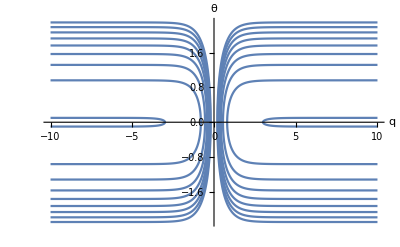

```mathematica
Clear[α,H0];
H0={2.01,3,4,5,6,7,8,9,10};
Plot[{ArcCosh[H0/(2 √(1+α^2 Csch[q ν]^2))],-ArcCosh[H0/(2 √(1+α^2 Csch[q ν]^2))]}//.α->1//.ν->1,{q,-10,10},PlotPoints->1000,AxesLabel->{"q","θ"},ImageSize->Scaled[.5]]
```

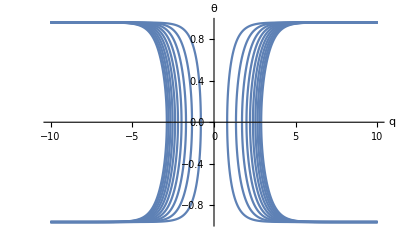

```mathematica
Clear[α,H0];
α={1,2,3,4,5,6,7,8,9,10};
Plot[{ArcCosh[H0/(2 √(1+α^2 Csch[q ν]^2))],-ArcCosh[H0/(2 √(1+α^2 Csch[q ν]^2))]}//.H0->3//.ν->1,{q,-10,10},PlotPoints->1000, PlotRange->All,AxesLabel->{"q","θ"},ImageSize->Scaled[.5]]
```

#### Weierstrass

```mathematica
Clear[AA]
```

```mathematica
H[x1_,x2_,p1_,p2_]:=(Cosh[p1]+Cosh[p2])(1+AA WeierstrassP[x1-x2,{ω1,ω2}])^(1/2)
```

```mathematica
dx1=D[H[x1,x2,p1,p2],p1]//FullSimplify
```

Sinh[p1] √(1+AA WeierstrassP[x1-x2,{3,3}])

```mathematica
dp1=-D[H[x1,x2,p1,p2],x1]//FullSimplify
```

-(AA (Cosh[p1]+Cosh[p2]) WeierstrassPPrime[x1-x2,{3,3}])/(2 √(1+AA WeierstrassP[x1-x2,{3,3}]))

```mathematica
eq1=dx1/.{x1->x[t],x2->-x[t],p1->p[t],p2->-p[t]}//FullSimplify
```

Sinh[p[t]] √(1+AA WeierstrassP[2 x[t],{3,3}])

```mathematica
eq2=dp1/.{x1->x[t],x2->-x[t],p1->p[t],p2->-p[t]}//FullSimplify
```

-(AA Cosh[p[t]] WeierstrassPPrime[2 x[t],{3,3}])/(√(1+AA WeierstrassP[2 x[t],{3,3}]))

```mathematica
DSolve[{eq1==x'[t],eq2==p'[t]},{x[t],p[t]},t]
```

{{x[t]→InverseFunction[Log[1+AA WeierstrassP[2 #1,{3,3}]]/(2 AA)&][C[1]-Log[Cosh[p[t]]]/AA],Solve[(Sech[K[1]] √(1+AA WeierstrassP[2 InverseFunction[Log[1+AA WeierstrassP[2 #1,{3,3}]]/(2 AA)&][C[1]-Log[Cosh[K[1]]]/AA],{3,3}]))/WeierstrassPPrime[2 InverseFunction[Log[1+AA WeierstrassP[2 #1,{3,3}]]/(2 AA)&][C[1]-Log[Cosh[K[1]]]/AA],{3,3}]K[1]1p[t]==-AA t+C[2],p[t]]}}

#### The scattering process + Results

```mathematica
Clear[t,ϵ,α,ν];
q[t_,ϵ_,α_,ν_]:=1/ν ArcCosh[Cosh[ArcSinh[α/Sqrt[ϵ^2-1]]] Cosh[2 ν Sqrt[ϵ^2-1] t]];
(*q[0,ϵ,α,ν]*)
Deltat[ϵ_,α_,ν_]:=-1/(2 ν Sqrt[ϵ^2-1]) Log[α^2/(ϵ^2-1)+1];
theta[t_,ϵ_,α_,ν_]:=ArcSinh[(√(-1+α^2+ϵ^2) Sinh[2 t √(-1+ϵ^2) ν])/(√(((α^2-1) (ϵ^2-1)+(-1+α^2+ϵ^2) (Cosh[2 t √(-1+ϵ^2) ν])^2)/(-1+ϵ^2)))];
x[t_,ϵ_,α_,ν_]:=1/(2 ν ϵ) ArcCosh[Cosh[ArcSinh[α/Sqrt[ϵ^2-1]]] Cosh[2 ν Sqrt[ϵ^2-1] t]];
(*p[t_,ϵ_,α_,ν_]:=Sinh[ArcSinh[(√2 √(-1+α^2+ϵ^2) Sinh[2 t √(-1+ϵ^2) ν])/(√((1-ϵ^2+α^2 (-1+2 ϵ^2)+(-1+α^2+ϵ^2) Cosh[4 t √(-1+ϵ^2) ν])/(-1+ϵ^2)))]];*)
(*Limit[p[t,ϵ,α,ν],t->Infinity]*)
```

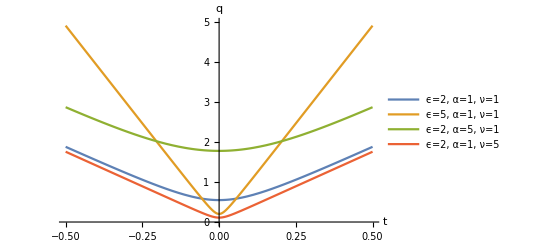

```mathematica
Plot[{q[t,2,1,1],q[t,5,1,1],q[t,2,5,1],q[t,2,1,5]},{t,-0.5,0.5},PlotLegends->{"ϵ=2, α=1, ν=1","ϵ=5, α=1, ν=1","ϵ=2, α=5, ν=1","ϵ=2, α=1, ν=5"},AxesLabel->{"t","q"},PlotRange->{{-0.5,0.5},{0,5}}]
```

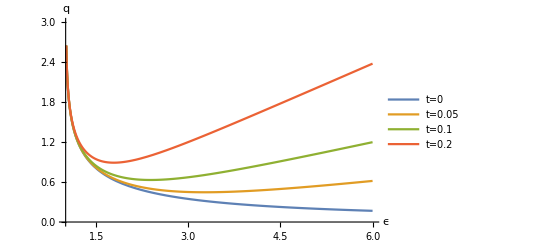

```mathematica
Plot[{q[0,ϵ,1,1],q[0.05,ϵ,1,1],q[0.1,ϵ,1,1],q[0.2,ϵ,1,1]},{ϵ,1.01,6},PlotLegends->{"t=0","t=0.05","t=0.1","t=0.2"},AxesLabel->{"ϵ","q"},PlotRange->{{1,6},{0,3}}]
```

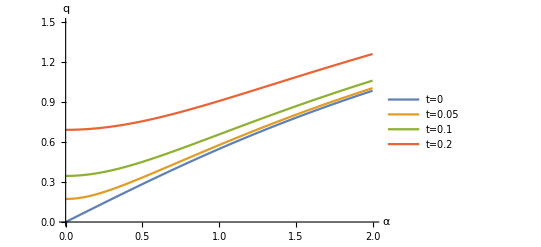

```mathematica
Plot[{q[0,2,α,1],q[0.05,2,α,1],q[0.1,2,α,1],q[0.2,2,α,1]},{α,0,2},PlotLegends->{"t=0","t=0.05","t=0.1","t=0.2"},AxesLabel->{"α","q"},PlotRange->{{0,2},{0,1.5}}]
```

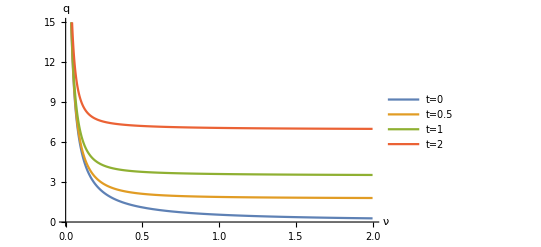

```mathematica
Plot[{q[0,2,1,ν],q[0.5,2,1,ν],q[1,2,1,ν],q[2,2,1,ν]},{ν,0,2},PlotLegends->{"t=0","t=0.5","t=1","t=2"},AxesLabel->{"ν","q"},PlotRange->{{0,2},{0,15}}]
```

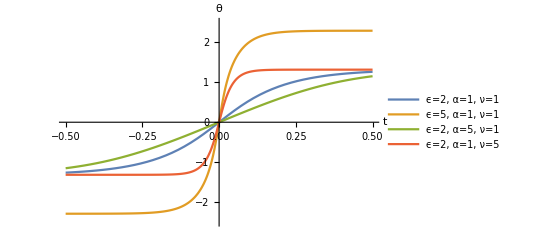

```mathematica
Plot[{theta[t,2,1,1],theta[t,5,1,1],theta[t,2,5,1],theta[t,2,1,5]},{t,-0.5,0.5},PlotLegends->{"ϵ=2, α=1, ν=1","ϵ=5, α=1, ν=1","ϵ=2, α=5, ν=1","ϵ=2, α=1, ν=5"},AxesLabel->{"t","θ"},PlotRange->{{-0.5,0.5},{-2.5,2.5}}]
```

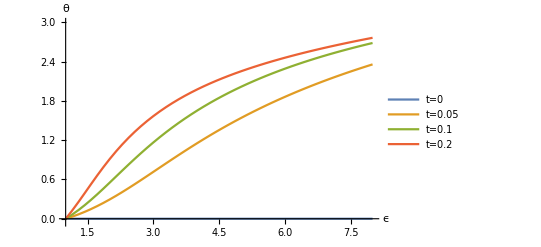

```mathematica
Plot[{theta[0,ϵ,1,1],theta[0.05,ϵ,1,1],theta[0.1,ϵ,1,1],theta[0.2,ϵ,1,1]},{ϵ,1.01,8},PlotLegends->{"t=0","t=0.05","t=0.1","t=0.2"},AxesLabel->{"ϵ","θ"},PlotRange->{{1,8},{-0.05,3}}]
```

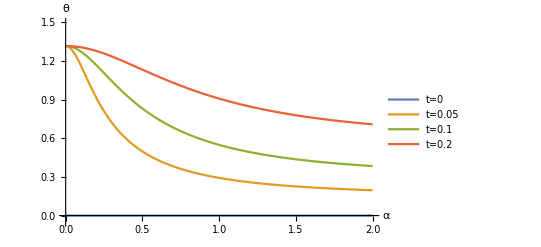

```mathematica
Plot[{theta[0,2,α,1],theta[0.05,2,α,1],theta[0.1,2,α,1],theta[0.2,2,α,1]},{α,0,2},PlotLegends->{"t=0","t=0.05","t=0.1","t=0.2"},AxesLabel->{"α","θ"},PlotRange->{{0,2},{-0.05,1.5}}]
```

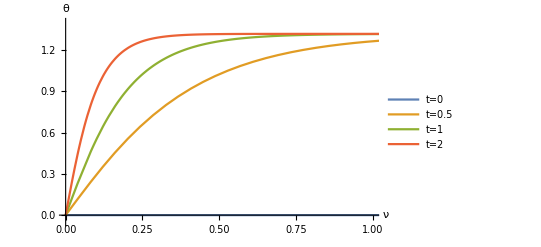

```mathematica
Plot[{theta[0,2,1,ν],theta[0.5,2,1,ν],theta[1,2,1,ν],theta[2,2,1,ν]},{ν,0,2},PlotLegends->{"t=0","t=0.5","t=1","t=2"},AxesLabel->{"ν","θ"},PlotRange->{{0,1},{-0.05,1.4}}]
```

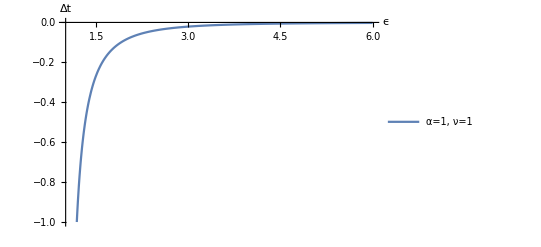

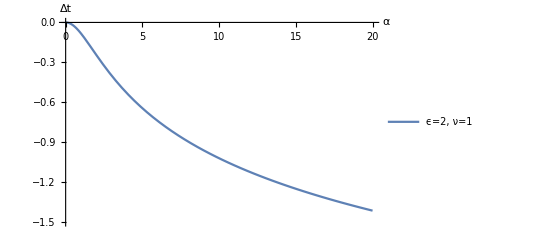

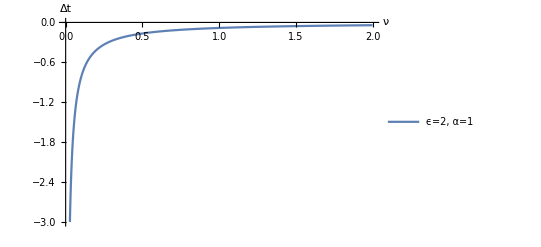

```mathematica
Plot[Deltat[ϵ,1,1],{ϵ,1.01,6},AxesLabel->{"ϵ","Δt"},PlotRange->{{1,6},{-1,0}},PlotLegends->{"α=1, ν=1"}]
Plot[Deltat[2,α,1],{α,0,20},AxesLabel->{"α","Δt"},PlotRange->{{0,20},{-1.5,0}},PlotLegends->{"ϵ=2, ν=1"}]
Plot[Deltat[2,1,ν],{ν,0,2},AxesLabel->{"ν","Δt"},PlotRange->{{0,2},{-3,0}},PlotLegends->{"ϵ=2, α=1"}]
```

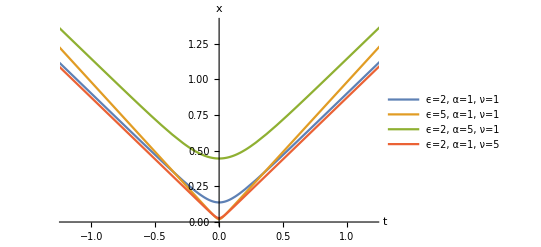

```mathematica
Plot[{x[t,2,1,1],x[t,5,1,1],x[t,2,5,1],x[t,2,1,5]},{t,-2,2},PlotLegends->{"ϵ=2, α=1, ν=1","ϵ=5, α=1, ν=1","ϵ=2, α=5, ν=1","ϵ=2, α=1, ν=5"},AxesLabel->{"t","x"},PlotRange->{{-1.2,1.2},{0,1.4}}]
```

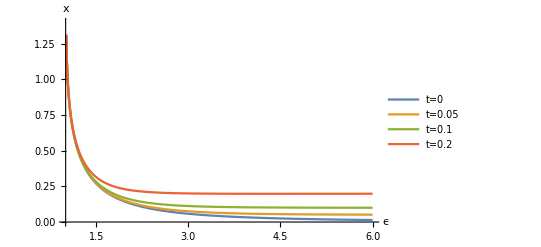

```mathematica
Plot[{x[0,ϵ,1,1],x[0.05,ϵ,1,1],x[0.1,ϵ,1,1],x[0.2,ϵ,1,1]},{ϵ,1.01,6},PlotLegends->{"t=0","t=0.05","t=0.1","t=0.2"},AxesLabel->{"ϵ","x"},PlotRange->{{1,6},{0,1.4}}]
```

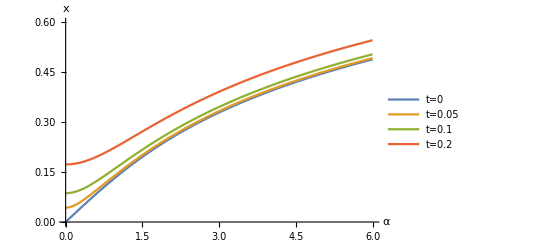

```mathematica
Plot[{x[0,2,α,1],x[0.05,2,α,1],x[0.1,2,α,1],x[0.2,2,α,1]},{α,0,6},PlotLegends->{"t=0","t=0.05","t=0.1","t=0.2"},AxesLabel->{"α","x"},PlotRange->{{0,6},{0,0.6}}]
```

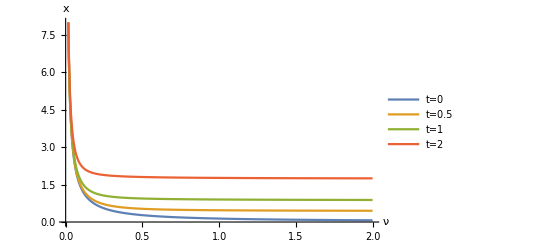

```mathematica
Plot[{x[0,2,1,ν],x[0.5,2,1,ν],x[1,2,1,ν],x[2,2,1,ν]},{ν,0,2},PlotLegends->{"t=0","t=0.5","t=1","t=2"},AxesLabel->{"ν","x"},PlotRange->{{0,2},{0,8}}]
```

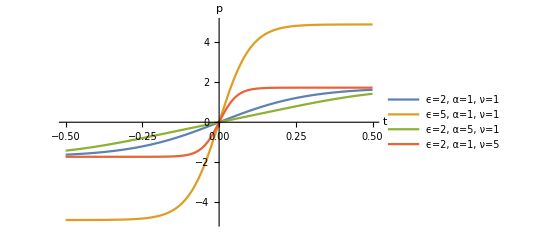

```mathematica
Plot[{p[t,2,1,1],p[t,5,1,1],p[t,2,5,1],p[t,2,1,5]},{t,-0.5,0.5},PlotLegends->{"ϵ=2, α=1, ν=1","ϵ=5, α=1, ν=1","ϵ=2, α=5, ν=1","ϵ=2, α=1, ν=5"},AxesLabel->{"t","p"},PlotRange->{{-0.5,0.5},{-5,5}}]
```

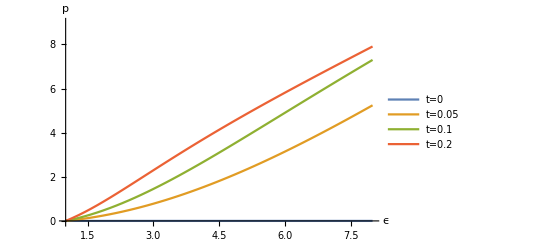

```mathematica
Plot[{p[0,ϵ,1,1],p[0.05,ϵ,1,1],p[0.1,ϵ,1,1],p[0.2,ϵ,1,1]},{ϵ,1.01,8},PlotLegends->{"t=0","t=0.05","t=0.1","t=0.2"},AxesLabel->{"ϵ","p"},PlotRange->{{1,8},{-0.05,9}}]
```

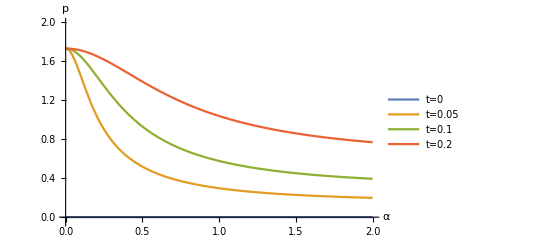

```mathematica
Plot[{p[0,2,α,1],p[0.05,2,α,1],p[0.1,2,α,1],p[0.2,2,α,1]},{α,0,2},PlotLegends->{"t=0","t=0.05","t=0.1","t=0.2"},AxesLabel->{"α","p"},PlotRange->{{0,2},{-0.05,2}}]
```

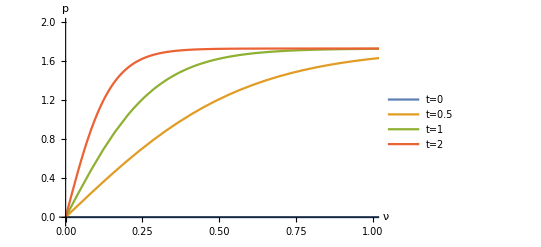

```mathematica
Plot[{p[0,2,1,ν],p[0.5,2,1,ν],p[1,2,1,ν],p[2,2,1,ν]},{ν,0,2},PlotLegends->{"t=0","t=0.5","t=1","t=2"},AxesLabel->{"ν","p"},PlotRange->{{0,1},{-0.05,2}}]
```

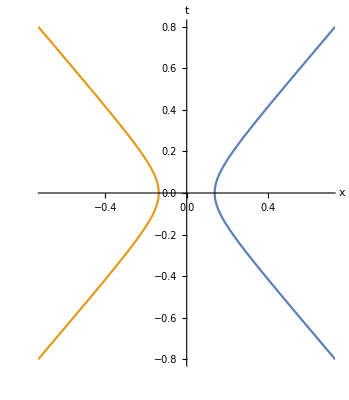

```mathematica
ParametricPlot[{{x[t,2,1,1],t},{-x[t,2,1,1],t}},{t,-0.8,0.8},AxesLabel->{"x","t"},PlotRange->{{-0.7,0.7},{-0.8,0.8}}]
```

```mathematica
Clear[ϵ,α,ν];
x1[t_,ϵ_,α_,ν_]:=1/(2 ν ϵ) Log[Sqrt[α^2/(ϵ^2-1)+1]]+1/ϵ Sqrt[ϵ^2-1] t;
x2[t_,ϵ_,α_,ν_]:=-1/(2 ν ϵ) Log[Sqrt[α^2/(ϵ^2-1)+1]]+1/ϵ Sqrt[ϵ^2-1] t;
x3[t_,ϵ_,α_,ν_]:=1/(2 ν ϵ) Log[Sqrt[α^2/(ϵ^2-1)+1]]-1/ϵ Sqrt[ϵ^2-1] t;
x4[t_,ϵ_,α_,ν_]:=-1/(2 ν ϵ) Log[Sqrt[α^2/(ϵ^2-1)+1]]-1/ϵ Sqrt[ϵ^2-1] t;
DELTAT[t_,ϵ_,α_,ν_]:=0.5;
(*RANGE[ϵ_,α_,ν_]:=1/ν Log[Sqrt[α^2/(ϵ^2-1)+1]]/(2 ν Sqrt[ϵ^2-1]);*)
Tlower[ϵ_,α_,ν_]:=(Cosh[Log[ϵ+Sqrt[ϵ^2-1]]]-1/ν Log[Sqrt[α^2/(ϵ^2-1)+1]])/(2 ν Sqrt[ϵ^2-1]);
Tupper[ϵ_,α_,ν_]:=(Cosh[Log[ϵ+Sqrt[ϵ^2-1]]]+1/ν Log[Sqrt[α^2/(ϵ^2-1)+1]])/(2 ν Sqrt[ϵ^2-1]);
```

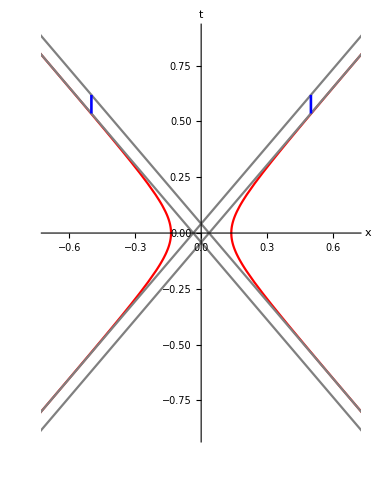

```mathematica
Show[ParametricPlot[{{x[t,2,1,1],t},{-x[t,2,1,1],t},{x1[t,2,1,1],t},{x2[t,2,1,1],t},{x3[t,2,1,1],t},{x4[t,2,1,1],t}},{t,-1.2,1.2},AxesLabel->{"x","t"},PlotRange->{{-0.7,0.7},{-0.9,0.9}},PlotStyle->{Red,Red,Gray,Gray,Gray,Gray}],ParametricPlot[{DELTAT[t,2,1,1],t},{t,Tlower[2,1,1],Tupper[2,1,1]},PlotStyle->{Thickness[0.005],Blue}],ParametricPlot[{-DELTAT[t,2,1,1],t},{t,Tlower[2,1,1],Tupper[2,1,1]},PlotStyle->{Thickness[0.005],Blue}]]
```

```mathematica
Clear[Phi1,PhiSS,PhiSAS];
Phi1[x_,β_,v_]:=4/β ArcTan[Exp[-γ x]]//.γ->1/(√(1-v^2));
PhiSS[x_,t_,β_,v_]:=4/β ArcTan[(v Sinh[x γ])/Cosh[v t γ]]//.γ->1/(√(1-v^2));
PhiSAS[x_,t_,β_,v_]:=4/β ArcTan[Sinh[v t γ]/(v Cosh[x γ])]//.γ->1/(√(1-v^2));
```

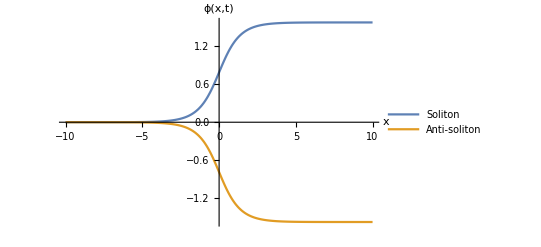

```mathematica
Plot[{Phi1[-x,4,0.5],Phi1[x,4,0.5]-π/2},{x,-10,10},PlotLegends->{"Soliton","Anti-soliton"},AxesLabel->{"x","ϕ(x,t)"}]
```

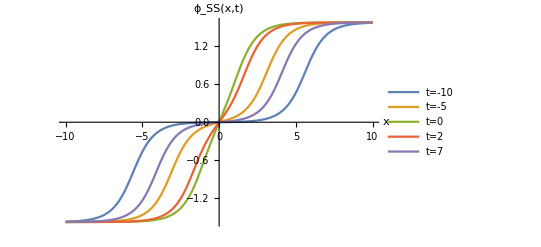

```mathematica
Plot[{PhiSS[x,-10,4,0.5],PhiSS[x,-5,4,0.5],PhiSS[x,0,4,0.5],PhiSS[x,2,4,0.5],PhiSS[x,7,4,0.5]},{x,-10,10},PlotLegends->{"t=-10","t=-5","t=0","t=2","t=7"},AxesLabel->{"x","ϕ_SS(x,t)"}]
```

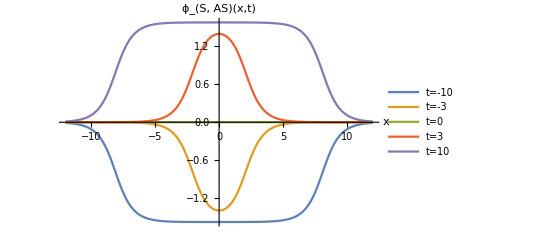

```mathematica
Plot[{PhiSAS[x,-15,4,0.5],PhiSAS[x,-3,4,0.5],PhiSAS[x,0,4,0.5],PhiSAS[x,3,4,0.5],PhiSAS[x,15,4,0.5]},{x,-12,12},PlotLegends->{"t=-10","t=-3","t=0","t=3","t=10"},AxesLabel->{"x","ϕ_(S, AS)(x,t)"}]
```

```mathematica
H2[q1_,q2_,p1_,p2_]:=(Cosh[p1]+Cosh[p2]) Abs[Coth[(q1-q2)/2]];
P2[q1_,q2_,p1_,p2_]:=(Sinh[p1]+Sinh[p2]) Abs[Coth[(q1-q2)/2]];
u1[t_,x_,q1_,q2_,p1_,p2_]:=Exp[t H2[q1,q2,p1,p2]-x P2[q1,q2,p1,p2]];
u2[t_,x_,q1_,q2_,p1_,p2_]:=Exp[t H2[q1,q2,p1,p2]-x P2[q1,q2,p1,p2]];
Phi2[t_,x_,q1_,q2_,p1_,p2_]:=4 ArcTan[(Exp[u1[t,x,q1,q2,p1,p2]]+Exp[u2[t,x,q1,q2,p1,p2]])/(1-Exp[u1[t,x,q1,q2,p1,p2]+u2[t,x,q1,q2,p1,p2]])];
```

```mathematica
Clear[u1,u2];
Sin[ArcTan[(Exp[u1]+Exp[u2])/(1-Exp[u1+u2])]]//FullSimplify
```

-(ⅇ^u1+ⅇ^u2)/((-1+ⅇ^(u1+u2)) √(Cosh[u1] Cosh[u2] Csch[(u1+u2)/2]^2))

```mathematica
Integrate[Sqrt[ϵ^2-1-α^2/(Sinh[ν 1/ν ArcCosh[Cosh[ArcSinh[α/Sqrt[ϵ^2-1]]] Cosh[2 ν Sqrt[ϵ^2-1] t]]])^2],t,Assumptions->ϵ^2>1,Assumptions->α>=0]//FullSimplify
```

1/(2 √2 √(-1+ϵ^2) √(-1+α^2+ϵ^2) ν)√(-1+ϵ^2-(α^2 (-1+ϵ^2))/(1-ϵ^2+(-1+α^2+ϵ^2) Cosh[2 t √(-1+ϵ^2) ν]^2)) √(1+α^2-ϵ^2+(-1+α^2+ϵ^2) Cosh[4 t √(-1+ϵ^2) ν]) Csch[2 t √(-1+ϵ^2) ν] Log[√2 √(-1+α^2+ϵ^2) Cosh[2 t √(-1+ϵ^2) ν]+√(1+α^2-ϵ^2+(-1+α^2+ϵ^2) Cosh[4 t √(-1+ϵ^2) ν])]

```mathematica
Integrate[(√2 √(-1+α^2+ϵ^2) Sinh[2 t √(-1+ϵ^2) ν])/(√((1-ϵ^2+α^2 (-1+2 ϵ^2)+(-1+α^2+ϵ^2) Cosh[4 t √(-1+ϵ^2) ν])/(-1+ϵ^2))) Sqrt[1+α^2/(Sinh[ν 1/ν ArcCosh[Cosh[ArcSinh[α/Sqrt[ϵ^2-1]]] Cosh[2 ν Sqrt[ϵ^2-1] t]]])^2],t]//FullSimplify
```

(√(((-1+α^2) (-1+ϵ^2)+(-1+α^2+ϵ^2) Cosh[2 t √(-1+ϵ^2) ν]^2)/(1-ϵ^2+(-1+α^2+ϵ^2) Cosh[2 t √(-1+ϵ^2) ν]^2)) √(1+α^2-ϵ^2+(-1+α^2+ϵ^2) Cosh[4 t √(-1+ϵ^2) ν]) Log[√2 √(-1+α^2+ϵ^2) Cosh[2 t √(-1+ϵ^2) ν]+√(1+α^2-ϵ^2+(-1+α^2+ϵ^2) Cosh[4 t √(-1+ϵ^2) ν])])/(2 √(-1+ϵ^2) ν √((1-ϵ^2+α^2 (-1+2 ϵ^2)+(-1+α^2+ϵ^2) Cosh[4 t √(-1+ϵ^2) ν])/(-1+ϵ^2)))

```mathematica
Solve[xe==1/(2 ν ϵ) Log[Sqrt[2] (Sqrt[α^2+ϵ^2-1]+α)],ϵ]
```

```mathematica
Series[(√(((-1+α^2) (-1+ϵ^2)+(-1+α^2+ϵ^2) Cosh[2 t √(-1+ϵ^2) ν]^2)/(1-ϵ^2+(-1+α^2+ϵ^2) Cosh[2 t √(-1+ϵ^2) ν]^2)) √(1+α^2-ϵ^2+(-1+α^2+ϵ^2) Cosh[4 t √(-1+ϵ^2) ν]) Log[√2 √(-1+α^2+ϵ^2) Cosh[2 t √(-1+ϵ^2) ν]+√(1+α^2-ϵ^2+(-1+α^2+ϵ^2) Cosh[4 t √(-1+ϵ^2) ν])])/(2 √(-1+ϵ^2) ν √((1-ϵ^2+α^2 (-1+2 ϵ^2)+(-1+α^2+ϵ^2) Cosh[4 t √(-1+ϵ^2) ν])/(-1+ϵ^2))),t->Infinity]//FullSimplify
```

(√(((-1+α^2) (-1+ϵ^2)+(-1+α^2+ϵ^2) Cosh[2 √(-1+ϵ^2) ν t+O[1/t]^2]^2)/(1-ϵ^2+(-1+α^2+ϵ^2) Cosh[2 √(-1+ϵ^2) ν t+O[1/t]^2]^2)) √(1+α^2-ϵ^2+(-1+α^2+ϵ^2) Cosh[4 √(-1+ϵ^2) ν t+O[1/t]^2]) Log[√2 √(-1+α^2+ϵ^2) Cosh[2 √(-1+ϵ^2) ν t+O[1/t]^2]+√(1+α^2-ϵ^2+(-1+α^2+ϵ^2) Cosh[4 √(-1+ϵ^2) ν t+O[1/t]^2])])/(2 √(-1+ϵ^2) ν √((1-ϵ^2+α^2 (-1+2 ϵ^2)+(-1+α^2+ϵ^2) Cosh[4 √(-1+ϵ^2) ν t+O[1/t]^2])/(-1+ϵ^2)))

```mathematica
Series[(√(((-1+α^2) (-1+ϵ^2)+(-1+α^2+ϵ^2) Cosh[2 t √(-1+ϵ^2) ν]^2)/(1-ϵ^2+(-1+α^2+ϵ^2) Cosh[2 t √(-1+ϵ^2) ν]^2)) √(1+α^2-ϵ^2+(-1+α^2+ϵ^2) Cosh[4 t √(-1+ϵ^2) ν]) Log[√2 √(-1+α^2+ϵ^2) Cosh[2 t √(-1+ϵ^2) ν]+√(1+α^2-ϵ^2+(-1+α^2+ϵ^2) Cosh[4 t √(-1+ϵ^2) ν])])/(2 √(-1+ϵ^2) ν √((1-ϵ^2+α^2 (-1+2 ϵ^2)+(-1+α^2+ϵ^2) Cosh[4 t √(-1+ϵ^2) ν])/(-1+ϵ^2))),t->-Infinity,Assumptions->ϵ^2-1>0,Assumptions->α^2>0,Assumptions->ν>0]//FullSimplify
```

(√(((-1+α^2) (-1+ϵ^2)+(-1+α^2+ϵ^2) Cosh[2 √(-1+ϵ^2) ν t+O[1/t]^2]^2)/(1-ϵ^2+(-1+α^2+ϵ^2) Cosh[2 √(-1+ϵ^2) ν t+O[1/t]^2]^2)) √(1+α^2-ϵ^2+(-1+α^2+ϵ^2) Cosh[4 √(-1+ϵ^2) ν t+O[1/t]^2]) Log[√2 √(-1+α^2+ϵ^2) Cosh[2 √(-1+ϵ^2) ν t+O[1/t]^2]+√(1+α^2-ϵ^2+(-1+α^2+ϵ^2) Cosh[4 √(-1+ϵ^2) ν t+O[1/t]^2])])/(2 ν √(1-ϵ^2+α^2 (-1+2 ϵ^2)+(-1+α^2+ϵ^2) Cosh[4 √(-1+ϵ^2) ν t+O[1/t]^2]))

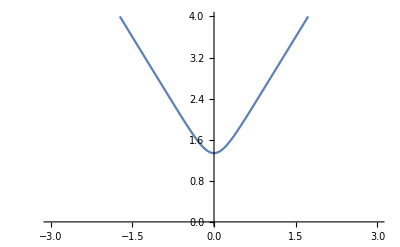

```mathematica
Plot[(√(((-1+α^2) (-1+ϵ^2)+(-1+α^2+ϵ^2) Cosh[2 t √(-1+ϵ^2) ν]^2)/(1-ϵ^2+(-1+α^2+ϵ^2) Cosh[2 t √(-1+ϵ^2) ν]^2)) √(1+α^2-ϵ^2+(-1+α^2+ϵ^2) Cosh[4 t √(-1+ϵ^2) ν]) Log[√2 √(-1+α^2+ϵ^2) Cosh[2 t √(-1+ϵ^2) ν]+√(1+α^2-ϵ^2+(-1+α^2+ϵ^2) Cosh[4 t √(-1+ϵ^2) ν])])/(2 √(-1+ϵ^2) ν √((1-ϵ^2+α^2 (-1+2 ϵ^2)+(-1+α^2+ϵ^2) Cosh[4 t √(-1+ϵ^2) ν])/(-1+ϵ^2)))//.α->5//.ϵ->2//.ν->1,{t,-3,3},PlotRange->{{-3,3},{0,4}}]
```

```mathematica
Integrate[Log[(EE^2-1)/EE^2]/(Sqrt[U-EE] Sqrt[EE^2-1]),{EE,2,3}]
```

∫_2^3 Log[(-1+EE^2)/EE^2]/(√(-1+EE^2) √(-EE+U))ⅆEE

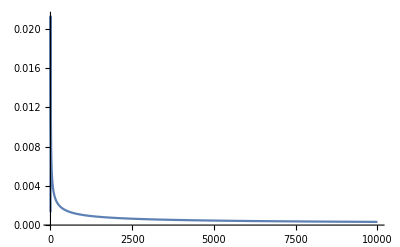

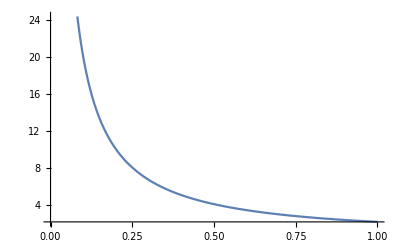

```mathematica
(*ParametricPlot[{{x[t,2,1,1],t},{-x[t,2,1,1],t}},{t,-1.2,1.2},AxesLabel->{"x","t"},PlotRange->{{-2,2},{-1,1}}]*)
Plot[-1/(π Sqrt[2]) NIntegrate[Log[(EE^2-1)/EE^2]/(Sqrt[U-EE] Sqrt[EE^2-1]),{EE,2,U}],{U,2.0001,10000},PlotRange->Full]
Plot[(1+α^2/Sinh[ν x]^2)^(1/2)//.α->1//.ν->1/2,{x,0,1}]
```

```mathematica
Plot[(1+(α^2/Sinh[x]^2))^(1/2)//.α->1,{x,-1,1},PlotRange->{1,10},AxesLabel->{"q","f(q)"},Axes->True, Ticks->False]
```

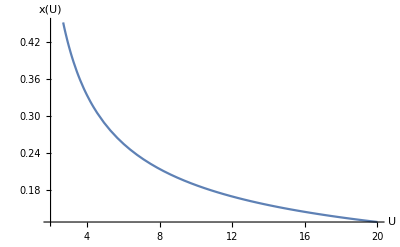

```mathematica
Plot[-1/(π Sqrt[2]) NIntegrate[Log[(EE^2-1)/EE^2]/(Sqrt[U-EE] Sqrt[EE^2-1]),{EE,1,U}],{U,2,20},AxesLabel->{"U","x(U)"}]
```

```mathematica
theta[t_,ϵ_,α_,ν_]:=ArcSinh[(√2 √(-1+α^2+ϵ^2) Sinh[2 t √(-1+ϵ^2) ν])/(√((1-ϵ^2+α^2 (-1+2 ϵ^2)+(-1+α^2+ϵ^2) Cosh[4 t √(-1+ϵ^2) ν])/(-1+ϵ^2)))];
(*x[t_,ϵ_,α_,ν_]:=1/(ν ϵ) ArcCosh[Cosh[ArcSinh[α/Sqrt[ϵ^2-1]]] Cosh[2 ν Sqrt[ϵ^2-1] t]];*)
s1[x_,t_,θ_,x0_]:=x Cosh[θ]+t Sinh[θ]-x0;
s2[x_,t_,θ_,x0_]:=x Cosh[θ]+-t Sinh[θ]+x0;
Ds[θ_]:=Log[(Tanh[θ])^2];
(*Phi2ss[x_,t_,ϵ_,α_,ν_,x0_,β_]:=4/β ArcTan[(Exp[s1[x,t,theta[t,ϵ,α,ν],x0]]+Exp[s2[x,t,theta[t,ϵ,α,ν],x0]])/(1-Exp[s1[x,t,theta[t,ϵ,α,ν],x0]+s2[x,t,theta[t,ϵ,α,ν],x0]+Ds[theta[t,ϵ,α,ν]]])];*)
Phi2ss[x_,t_,ϵ_,α_,ν_,x0_,β_]:=
```

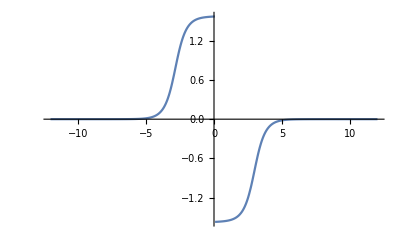

```mathematica
Plot[Phi2ss[x,5,2,1,1/2,3,4],{x,-12,12},PlotRange->Full]
```

```mathematica
q1[x_,t_,ϵ_,α_,ν_,q10_]:=ϵ x+1/ν ArcCosh[Cosh[ArcSinh[α/Sqrt[ϵ^2-1]]] Cosh[2 ν Sqrt[ϵ^2-1] t]]+q10;
q2[x_,t_,ϵ_,α_,ν_,q20_]:=ϵ x-1/ν ArcCosh[Cosh[ArcSinh[α/Sqrt[ϵ^2-1]]] Cosh[2 ν Sqrt[ϵ^2-1] t]]+q20;
Phi2RS[x_,t_,ϵ_,α_,ν_,q10_,q20_]:=4 ArcTan[(Exp[q1[x,t,ϵ,α,ν,q10]]+Exp[q2[x,t,ϵ,α,ν,q20]])/(1-Exp[q1[x,t,ϵ,α,ν,q10]+q2[x,t,ϵ,α,ν,q20]])];
```

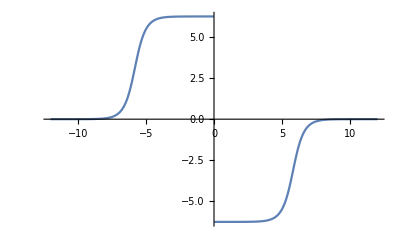

```mathematica
Plot[Phi2RS[x,5,2,1,1/2,-6,6],{x,-12,12},PlotRange->Full]
```

```mathematica
Clear[α,ϵ,ν,x,t];
-4 ArcTan[(Cosh[ArcSinh[α/Sqrt[ϵ^2-1]]] Cosh[2 ν Sqrt[ϵ^2-1] t])/Sinh[ν ϵ x]]
```

-4 ArcTan[√(1+α^2/(-1+ϵ^2)) Cosh[2 t √(-1+ϵ^2) ν] Csch[x ϵ ν]]

```mathematica
Cosh[ArcSinh[α/Sqrt[ϵ^2-1]]]
```

√(1+α^2/(-1+ϵ^2))

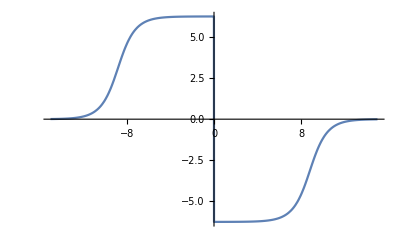

```mathematica
Plot[-4 ArcTan[√(1+α^2/(-1+ϵ^2))Cosh[2 ν Sqrt[ϵ^2-1] t]/Sinh[ν ϵ x]]//.α->1//.ν->1/2//.t->-5//.ϵ->2,{x,-15,15}]
```

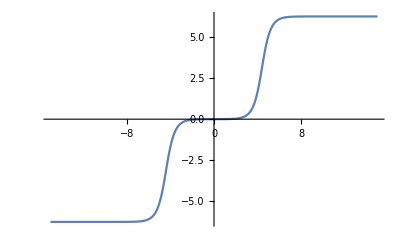

```mathematica
Plot[4/β ArcTan[(v Sinh[ϵ x])/Cosh[ϵ v t]]//.β->1//.t->-5//.v->Tanh[ArcCosh[ϵ]]//.ϵ->2,{x,-15,15}]
```

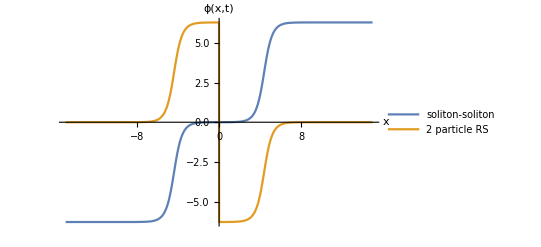

```mathematica
(*2 soliton, 2 particle RS*)
Plot[{4 ArcTan[Tanh[TV] Sinh[Cosh[TV] x]/Cosh[Sinh[TV] t]]//.TV->ArcCosh[ϵ]//.t->-5//.ϵ->2,-4 ArcTan[1/Tanh[TV] Cosh[Sinh[TV] t]/Sinh[Cosh[TV] x]]//.TV->ArcCosh[ϵ]//.t->-5//.ϵ->2},{x,-15,15},PlotLegends->{"soliton-soliton","2 particle RS"},AxesLabel->{"x","ϕ(x,t)"}]
```

```mathematica
D[Sqrt[1-α^2/(Cosh[ν q])^2],q]//FullSimplify
```

(α^2 ν Sech[q ν]^2 Tanh[q ν])/(√(1-α^2 Sech[q ν]^2))

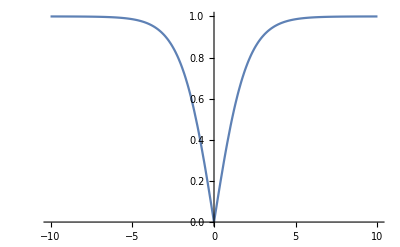

```mathematica
Plot[Sqrt[1-α^2/(Cosh[ν q])^2]//.α->1//.ν->1/2,{q,-10,10},PlotRange->Full]
```

```mathematica
Integrate[1/Sqrt[1-z^2],{z,1,Sinh[ν q]/Sinh[ν qe]}]//FullSimplify
```

ConditionalExpression[-ArcCos[Csch[qe ν] Sinh[q ν]], Csch[qe ν]^2 Sinh[q ν]^2≤1]

```mathematica
Integrate[1/Sqrt[1-z^2],z]//FullSimplify
```

ArcSin[z]

```mathematica
qq[t_]:=1/ν ArcSinh[Sqrt[(α^2+ϵ^2-1)/(1-ϵ^2)] Cos[2 ν Sqrt[1-ϵ^2] t]];
ArcSinh[D[qq[t],t]/(2 Sqrt[1-α^2/(Cosh[ν 1/ν ArcSinh[Sqrt[(α^2+ϵ^2-1)/(1-ϵ^2)] Cos[2 ν Sqrt[1-ϵ^2] t]]])^2])]//FullSimplify
```

-ArcSinh[(√(1-ϵ^2) √(-(-1+α^2+ϵ^2)/(-1+ϵ^2)) Sin[2 t √(1-ϵ^2) ν])/(√(1-((-1+α^2+ϵ^2) Cos[2 t √(1-ϵ^2) ν]^2)/(-1+ϵ^2)) √(1+(α^2 (-1+ϵ^2))/(1-ϵ^2+(-1+α^2+ϵ^2) Cos[2 t √(1-ϵ^2) ν]^2)))]

```mathematica
qq[t_]:=1/ν ArcCosh[Cosh[ArcSinh[α/Sqrt[ϵ^2-1]]] Cosh[2 ν Sqrt[ϵ^2-1] t]];
D[qq[t],t]/(2 Sqrt[1+α^2/(Sinh[ν 1/ν ArcCosh[Cosh[ArcSinh[α/Sqrt[ϵ^2-1]]] Cosh[2 ν Sqrt[ϵ^2-1] t]]])^2])//FullSimplify
```

(√(-1+ϵ^2) √(1+α^2/(-1+ϵ^2)) Sinh[2 t √(-1+ϵ^2) ν])/(√(-1+√(1+α^2/(-1+ϵ^2)) Cosh[2 t √(-1+ϵ^2) ν]) √(1+√(1+α^2/(-1+ϵ^2)) Cosh[2 t √(-1+ϵ^2) ν]) √(1+(α^2 (-1+ϵ^2))/(1-ϵ^2+(-1+α^2+ϵ^2) Cosh[2 t √(-1+ϵ^2) ν]^2)))

```mathematica
Cosh[ArcSinh[x]]
```

√(1+x^2)

```mathematica
Integrate[1/Sqrt[z^2-1],{z,1,Sinh[ν qqq]/Sinh[ν qe]}]//FullSimplify
```

ConditionalExpression[1/2 (ⅈ π+Log[1-(2 ⅇ^(qe ν) Sinh[qqq ν])/(√(-1-ⅇ^(4 qe ν)+ⅇ^(2 (qe-qqq) ν)+ⅇ^(2 (qe+qqq) ν)) Sign[1-ⅇ^(2 qe ν)])]-Log[1-(2 ⅇ^(qe ν) Sinh[qqq ν])/(√(-1-ⅇ^(4 qe ν)+ⅇ^(2 (qe-qqq) ν)+ⅇ^(2 (qe+qqq) ν)) Sign[-1+ⅇ^(2 qe ν)])]), Csch[qe ν] Sinh[qqq ν]≥1]

```mathematica
Integrate[1/Sqrt[1+z^2],z]//FullSimplify
```

ArcSinh[z]

```mathematica
ArcSinh[0]
```

0

```mathematica
Clear[q];
q[t_]:=1/ν ArcSinh[Sqrt[(α^2+ϵ^2-1)/(ϵ^2-1)] Sinh[2 ν Sqrt[ϵ^2-1] t]];
D[q[t],t]/(2 Sqrt[1-α^2/((Cosh[ν 1/ν ArcSinh[Sqrt[(α^2+ϵ^2-1)/(ϵ^2-1)] Sinh[2 ν Sqrt[ϵ^2-1] t]]])^2)])//FullSimplify
```

(√(-1+ϵ^2) √((-1+α^2+ϵ^2)/(-1+ϵ^2)) Cosh[2 t √(-1+ϵ^2) ν])/(√(1+((-1+α^2+ϵ^2) Sinh[2 t √(-1+ϵ^2) ν]^2)/(-1+ϵ^2)) √(1-α^2/(1+((-1+α^2+ϵ^2) Sinh[2 t √(-1+ϵ^2) ν]^2)/(-1+ϵ^2))))

```mathematica
Limit[ArcSinh[(√(-1+ϵ^2) √((-1+α^2+ϵ^2)/(-1+ϵ^2)) Cosh[2 t √(-1+ϵ^2) ν])/(√(1+((-1+α^2+ϵ^2) Sinh[2 t √(-1+ϵ^2) ν]^2)/(-1+ϵ^2)) √(1-α^2/(1+((-1+α^2+ϵ^2) Sinh[2 t √(-1+ϵ^2) ν]^2)/(-1+ϵ^2))))],t->Infinity]
```

ConditionalExpression[Log[√(-1+ϵ^2)+Abs[ϵ]], α^2+ϵ^2>1&&√(-1+ϵ^2) ν>0]

```mathematica
Cosh[ArcSinh[x]]
```

√(1+x^2)

```mathematica
Clear[ϵ,α,ν];
x[t_,ϵ_,α_,ν_]:=1/(2 ν ϵ)ArcSinh[Sqrt[(α^2+ϵ^2-1)/(ϵ^2-1)] Sinh[2 ν Sqrt[ϵ^2-1] t]];
x1[t_,ϵ_,α_,ν_]:=1/(2 ν ϵ) Log[Sqrt[(α^2+ϵ^2-1)/(ϵ^2-1)]]+1/ϵ Sqrt[ϵ^2-1] t;
x2[t_,ϵ_,α_,ν_]:=-1/(2 ν ϵ) Log[Sqrt[(α^2+ϵ^2-1)/(ϵ^2-1)]]+1/ϵ Sqrt[ϵ^2-1] t;
x3[t_,ϵ_,α_,ν_]:=1/(2 ν ϵ) Log[Sqrt[(α^2+ϵ^2-1)/(ϵ^2-1)]]-1/ϵ Sqrt[ϵ^2-1] t;
x4[t_,ϵ_,α_,ν_]:=-1/(2 ν ϵ) Log[Sqrt[(α^2+ϵ^2-1)/(ϵ^2-1)]]-1/ϵ Sqrt[ϵ^2-1] t;
DELTAT[t_,ϵ_,α_,ν_]:=0.4;
(*RANGE[ϵ_,α_,ν_]:=1/ν Log[Sqrt[α^2/(ϵ^2-1)+1]]/(2 ν Sqrt[ϵ^2-1]);*)
Tlower[x_,ϵ_,α_,ν_]:=ϵ/Sqrt[ϵ^2-1] x - Log[Sqrt[(α^2+ϵ^2-1)/(ϵ^2-1)]]/(2 ν Sqrt[ϵ^2-1]);
Tupper[x_,ϵ_,α_,ν_]:=ϵ/Sqrt[ϵ^2-1] x + Log[Sqrt[(α^2+ϵ^2-1)/(ϵ^2-1)]]/(2 ν Sqrt[ϵ^2-1]);
```

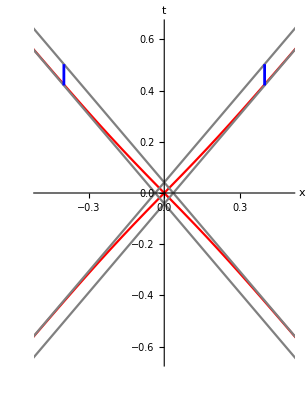

```mathematica
Show[ParametricPlot[{{x[t,2,1,1],t},{-x[t,2,1,1],t},{x1[t,2,1,1],t},{x2[t,2,1,1],t},{x3[t,2,1,1],t},{x4[t,2,1,1],t}},{t,-1.2,1.2},AxesLabel->{"x","t"},PlotRange->{{-0.5,0.5},{-0.65,0.65}},PlotStyle->{Red,Red,Gray,Gray,Gray,Gray}],ParametricPlot[{DELTAT[t,2,1,1],t},{t,Tlower[0.4,2,1,1],Tupper[0.4,2,1,1]},PlotStyle->{Thickness[0.005],Blue}],ParametricPlot[{-DELTAT[t,2,1,1],t},{t,Tlower[0.4,2,1,1],Tupper[0.4,2,1,1]},PlotStyle->{Thickness[0.005],Blue}]]
```

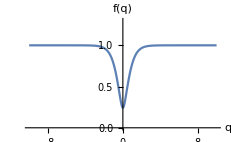

```mathematica
Plot[Sqrt[1-α^2/(Cosh[ν q])^2]//.α->0.97//.ν->1,{q,-10,10},AxesLabel->{"q","f(q)"},Axes->True, Ticks->False,PlotRange->{{-10,10},{0,1.3}}]
```

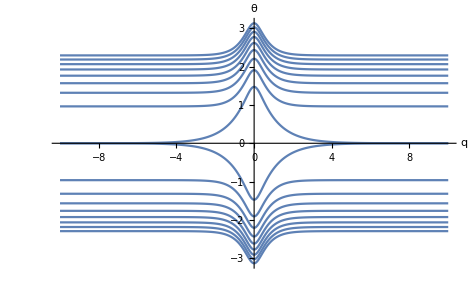

```mathematica
Clear[q,α,H0];
H0={2,3,4,5,6,7,8,9,10};
Plot[{ArcCosh[H0/(2 √(1-α^2/(Cosh[q ν])^2))],-ArcCosh[H0/(2 √(1-α^2/(Cosh[q ν])^2))]}//.α->0.9//.ν->1,{q,-10,10},PlotPoints->1000,AxesLabel->{"q","θ"},ImageSize->Scaled[.5]]
```

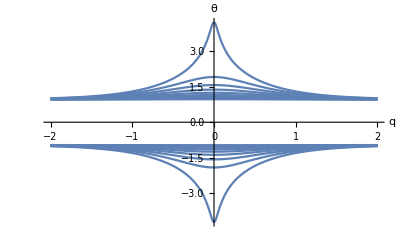

```mathematica
Clear[α,H0];
α={0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.999};
Plot[{ArcCosh[H0/(2 √(1+-α^2/(Cosh[q ν])^2))],-ArcCosh[H0/(2 √(1-α^2/(Cosh[q ν])^2))]}//.H0->3//.ν->1,{q,-2,2},PlotPoints->1000, PlotRange->All,AxesLabel->{"q","θ"},ImageSize->Scaled[.5],PlotRange->Full]
```